```mathematica
v="5";
p="0.1";
g5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l5k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number}];
v5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l5k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number}];
av5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l5k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];
g10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l10k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number}];
v10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l10k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number}];
av10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l10k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];
g20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l20k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number}];
v20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l20k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number}];
av20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l20k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];
g30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l30k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number}];
v30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l30k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number}];
av30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l30k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];
g50k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l50k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number}];
v50k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l50k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number}];
av50k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l50k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];
```

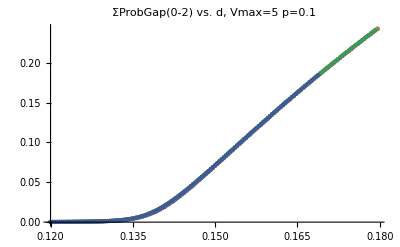

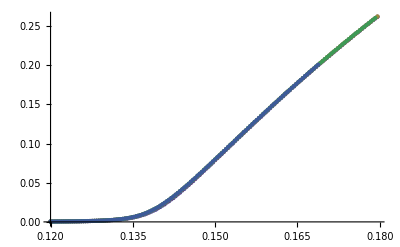

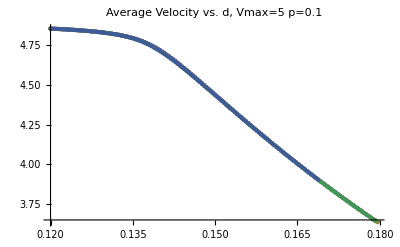

```mathematica
ngap="2";
nvel="2";
jj=StringToStream[ngap];
ng= Read[jj,Number];
ii=StringToStream[nvel];
nv= Read[ii,Number];
ClearAll[d0,z,α];
d0=0.0674;
z=0.65;
α=0.665;
gap5v5=Table[{g5k1[[All,1]][[j]],Sum[g5k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g5k1]}];
vel5v5=Table[{v5k1[[All,1]][[j]],Sum[v5k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v5k1]}];
avel5v5=Table[{av5k1[[All,1]][[j]],av5k1[[All,2]][[j]]},{j,1,Length[av5k1]}];
gap10v5=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g10k1]}];
vel10v5=Table[{v10k1[[All,1]][[j]],Sum[v10k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v10k1]}];
avel10v5=Table[{av10k1[[All,1]][[j]],av10k1[[All,2]][[j]]},{j,1,Length[av10k1]}];
gap20v5=Table[{g20k1[[All,1]][[j]],Sum[g20k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g20k1]}];
vel20v5=Table[{v20k1[[All,1]][[j]],Sum[v20k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v20k1]}];
avel20v5=Table[{av20k1[[All,1]][[j]],av20k1[[All,2]][[j]]},{j,1,Length[av20k1]}];
gap30v5=Table[{g30k1[[All,1]][[j]],Sum[g30k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g30k1]}];
vel30v5=Table[{v30k1[[All,1]][[j]],Sum[v30k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v30k1]}];
avel30v5=Table[{av30k1[[All,1]][[j]],av30k1[[All,2]][[j]]},{j,1,Length[av30k1]}];
gap50v5=Table[{g50k1[[All,1]][[j]],Sum[g50k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g50k1]}];
vel50v5=Table[{v50k1[[All,1]][[j]],Sum[v50k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v50k1]}];
avel50v5=Table[{av50k1[[All,1]][[j]],av50k1[[All,2]][[j]]},{j,1,Length[av50k1]}];
ListPlot[{gap5v5,gap10v5,gap20v5,gap30v5,gap50v5},PlotLabel->"ΣProbGap(0-"<>ngap<>") vs. d, Vmax="<>v<>"  p="<>p,PlotLegend->{"5k","10k","20k","30k","50k"},LegendPosition->{1.1,-0.4},LegendShadow->None]
ListPlot[{vel5v5,vel10v5,vel20v5,vel30v5,vel50v5}]
ListPlot[{avel5v5,avel10v5,avel20v5,avel30v5,avel50v5},PlotLabel->"Average Velocity vs. d, Vmax="<>v<>"  p="<>p,PlotLegend->{"5k","10k","20k","30k","50k"},LegendPosition->{1.1,-0.4},LegendShadow->None]
```

```mathematica
avel10v5
```

{{0.12,4.85578},{0.1204,4.85517},{0.1208,4.8543},{0.1212,4.85405},{0.1216,4.85323},{0.122,4.85237},{0.1224,4.85175},{0.1228,4.85104},{0.1232,4.85012},{0.1236,4.84917},{0.124,4.84851},{0.1244,4.84754},{0.1248,4.8464},{0.1252,4.84544},{0.1256,4.84417},{0.126,4.84287},{0.1264,4.84196},{0.1268,4.84117},{0.1272,4.83982},{0.1276,4.83826},{0.128,4.83721},{0.1284,4.836},{0.1288,4.83432},{0.1292,4.83274},{0.1296,4.83138},{0.13,4.82919},{0.1304,4.82756},{0.1308,4.82568},{0.1312,4.82383},{0.1316,4.82118},{0.132,4.81909},{0.1324,4.81649},{0.1328,4.81443},{0.1332,4.81145},{0.1336,4.80836},{0.134,4.80512},{0.1344,4.80149},{0.1348,4.79762},{0.1352,4.79357},{0.1356,4.78938},{0.136,4.78437},{0.1364,4.7793},{0.1368,4.7741},{0.1372,4.769},{0.1376,4.76226},{0.138,4.75519},{0.1384,4.74821},{0.1388,4.7405},{0.1392,4.73311},{0.1396,4.7248},{0.14,4.71492},{0.1404,4.70752},{0.1408,4.69808},{0.1412,4.68786},{0.1416,4.67866},{0.142,4.6676},{0.1424,4.65892},{0.1428,4.64631},{0.1432,4.63663},{0.1436,4.6254},{0.144,4.6149},{0.1444,4.6032},{0.1448,4.59199},{0.1452,4.58078},{0.1456,4.5698},{0.146,4.55737},{0.1464,4.54704},{0.1468,4.53384},{0.1472,4.52283},{0.1476,4.51041},{0.148,4.49791},{0.1484,4.48711},{0.1488,4.47407},{0.1492,4.46247},{0.1496,4.45062},{0.15,4.43923},{0.1504,4.42766},{0.1508,4.41521},{0.1512,4.40161},{0.1516,4.39055},{0.152,4.37783},{0.1524,4.36699},{0.1528,4.35455},{0.1532,4.34315},{0.1536,4.3308},{0.154,4.31902},{0.1544,4.30621},{0.1548,4.29533},{0.1552,4.28356},{0.1556,4.27153},{0.156,4.26041},{0.1564,4.24818},{0.1568,4.23651},{0.1572,4.22535},{0.1576,4.21473},{0.158,4.20183},{0.1584,4.19093},{0.1588,4.17837},{0.1592,4.16776},{0.1596,4.15628},{0.16,4.14446},{0.1604,4.13255},{0.1608,4.1219},{0.1612,4.11096},{0.1616,4.09912},{0.162,4.08753},{0.1624,4.0766},{0.1628,4.06575},{0.1632,4.05394},{0.1636,4.04385},{0.164,4.03225},{0.1644,4.02189},{0.1648,4.01047},{0.1652,4.00063},{0.1656,3.98909},{0.166,3.97846},{0.1664,3.96814},{0.1668,3.95732},{0.1672,3.94724},{0.1676,3.93566},{0.168,3.92579},{0.1684,3.91511},{0.1688,3.90436},{0.1692,3.89363},{0.1696,3.88362},{0.17,3.87319},{0.1704,3.86243},{0.1708,3.85348}}

```mathematica
gap1000=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,2,2}]},{j,1,Length[g10k1]}];
gap1001=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,3,3}]},{j,1,Length[g10k1]}];
gap1002=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,4,4}]},{j,1,Length[g10k1]}];
gap1003=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,5,5}]},{j,1,Length[g10k1]}];
gap1004=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,6,6}]},{j,1,Length[g10k1]}];
gap1005=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,7,7}]},{j,1,Length[g10k1]}];
```

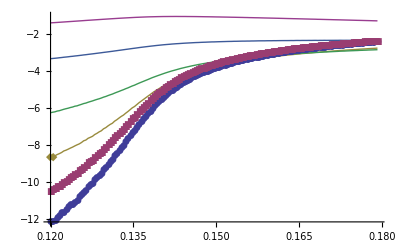

```mathematica
ListLogPlot[{gap1000,gap1001,gap1002,gap1003,gap1004,gap1005},PlotLegend->{"0","1","2","3","4","5"},LegendPosition->{1.1,-0.4},LegendShadow->None,Joined->{True},PlotMarkers->Automatic,PlotRange->Full,PlotLabel->"GapDistribution, Vmax=5, 30k"]
```

```mathematica
gapa1000=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,2,2}]},{j,1,Length[g10k1]}];
gapa1001=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,2,3}]},{j,1,Length[g10k1]}];
gapa1002=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,2,4}]},{j,1,Length[g10k1]}];
gapa1003=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,2,5}]},{j,1,Length[g10k1]}];
gapa1004=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,2,6}]},{j,1,Length[g10k1]}];
gapa1005=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,2,7}]},{j,1,Length[g10k1]}];
```